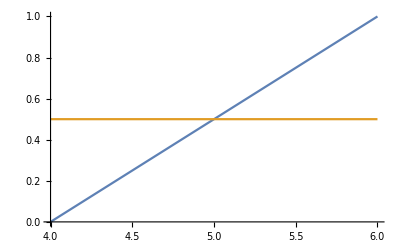
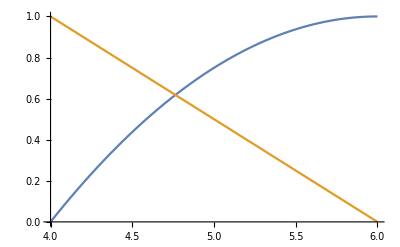
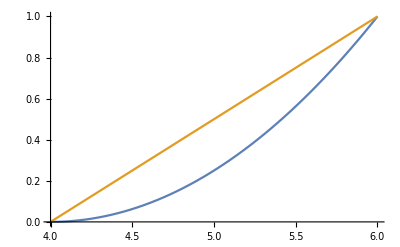
{-Graphics-,-Graphics-,-Graphics-,4,6}

```mathematica
m1:=b-a;
m2:=Sqrt[V]-(b-a);


uniformIntervalCDF[e_]:=Piecewise[{{(e-m1)/(m2-m1),m1<e<m2},{1, e>=m2},{0,x<=m1}}];
uniformIntervalPDF[e_]:= uniformIntervalCDF'[e];

increasingIntervalCDF[e_]:=Piecewise[{{((e-m1)/(m2-m1))^2,m1<e<m2},{1, e>=m2},{0,x<=m1}}];
increasingIntervalPDF[e_]:=increasingIntervalCDF'[e];

decreasingIntervalCDF[e_]:=Piecewise[{{((m1-e)(m1-2m2+e))/(m2-m1)^2,m1<e<m2},{1, e>=m2},{0,x<=m1}}];
decreasingIntervalPDF[e_]:=decreasingIntervalCDF'[e];


V:=100;
a:=-2; (*Set values for plotting*)
b:=2;

p1=Plot[{uniformIntervalCDF[e],uniformIntervalPDF[e]},{e,m1,m2}];
p2=Plot[{decreasingIntervalCDF[e],decreasingIntervalPDF[e]},{e,m1,m2}];
p3=Plot[{increasingIntervalCDF[e],increasingIntervalPDF[e]},{e,m1,m2}];
{p1,p2,p3,m1,m2}
(*p2=Plot[{increasingIntervalCDF[e],increasingIntervalCDF[e]},{e,m1,m2}, PlotLabel->increasing];
p3=Plot[{decreasingIntervalCDF[e],decreasingIntervalCDF[e]},{e,m1,m2}, PlotLabel->decreasing];
{p1}
```